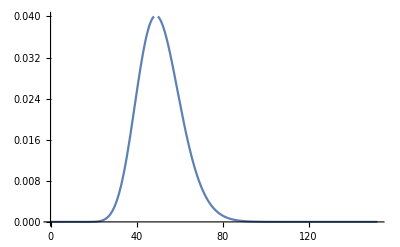

{y→97.3371}

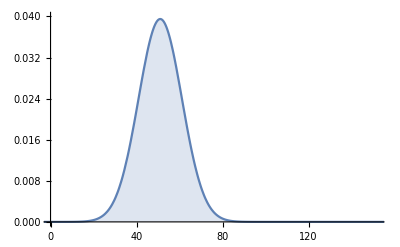

```mathematica
Clear[x,k,f,g,y]
k=51;
f[x_]:=1/(2^(k/2)Gamma[k/2])x^(-1+k/2)ⅇ^(-x/2);
Plot[f[x],{x,0,k+10 √(2k)},PlotRange->{{0,k+10 √(2k)},{0,0.04}}]
confidence = 0.9999;
g[y_]:=Integrate[f[x],{x,y,∞}] - (1-confidence);
FindRoot[g[y]==0,{y,80}]
Plot[Gamma[x],{x,0,10}];
Plot[PDF[NormalDistribution[k,√(2k)],x],{x,k-6k,k+6k},Filling->Axis,PlotRange->{{0,k+10 √(2k)},{0,0.04}}]
```